```mathematica
(*Clear all values*) 
ClearAll["`*"]

(*Set Directory*)
dir=SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Position of Wells; WS:Well size, CS:Cell size, LS: Loading size*)
Loading[WS_,CS_,LS_]:=Table[RandomInteger[{1,WS}],{LS},{CS}];

(*Number of Cells in the Each Well;*)
NoSCiW[WS_,CS_,LS_]:=Table[BinCounts[Loading[WS,CS,LS][[i]]],{i,1,LS}]

(*Number of Single Cells in the Each Loading*)
NoSC[WS_,CS_,LS_]:=Table[Count[BinCounts[Loading[WS,CS,LS][[i]]],1],{i,1,LS}]

(*Mean and SD of Single Cell Numbers in each Cell Size*)
Result[WS_,LS_]:=With[{list=Table[NoSC[WS,i,LS],{i,1,2WS}]},Table[{i,N[Mean[list[[i]]]], N[StandardDeviation[list[[i]]]]},{i,1,2WS}]]
```

```mathematica
(*Number of Wells*) NoW=64;
(*Number of Spiked Cells*) NoC=50;
(*Number of Loading Repeat*) NoL=100;

example=NoSCiW[NoW,NoC,1]
array={{cell number,mean,sd}};
results=Result[NoW,NoL];
efficiency=Table[{i,Part[results[[All,2]]/results[[All,1]],i]},{i,1,Length[results]}];
Do[AppendTo[array,results[[i]]],{i,1,Length[results]}]
```

{{0,2,0,0,0,4,0,0,1,1,1,0,1,0,0,1,0,1,2,0,0,1,1,0,1,1,1,1,1,0,0,1,2,0,3,1,1,0,0,1,2,2,0,1,1,0,1,3,0,2,1,2,0,1,0,1,0,0,0,1,1,0,0,0,1}}

```mathematica
Export["array.csv",array]
Export["efficiency.csv",efficiency]
```

array.csv

efficiency.csv

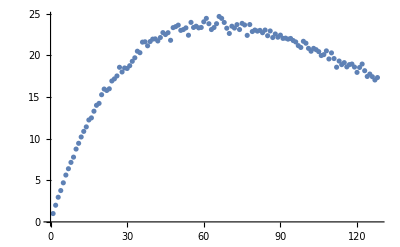

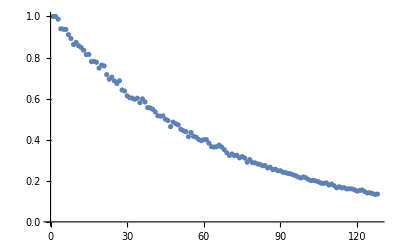

```mathematica
ListPlot[results[[All,1;;2]]]
ListPlot[efficiency]
```